```mathematica
d3a1={(√3)/2,1/2,0};
d3a2={(√3)/2,-1/2,0};
d3a3={0,0,1};
d3b1= Cross[d3a2,d3a3]/(d3a1.Cross[d3a2,d3a3]);
d3b2=Cross[d3a3,d3a1]/(d3a2.Cross[d3a3,d3a1]);
a1=Drop[d3a1,-1]
a2=Drop[d3a2,-1]
a3=Drop[d3a3,-1]
b1=Drop[d3b1,-1]
b2=Drop[d3b2,-1]
```

{(√3)/2,1/2}

{(√3)/2,-1/2}

{0,0}

{1/(√3),1}

{1/(√3),-1}

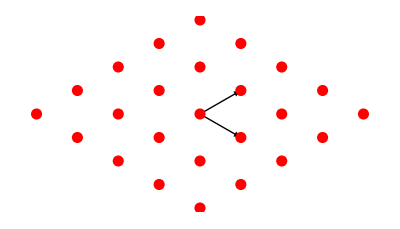

```mathematica
p0={0,0};
directLatticeVectors[n1_,n2_]:=n1 a1+n2 a2
reciprocalLatticeVectors[nk1_,nk2_]:=nk1 b1+nk2 b2

tableBLV[nn1_,nn2_]:=Flatten[Table[Table[directLatticeVectors[n1,n2],{n1,-nn1,nn1}],{n2,-nn2,nn2}],1]
Graphics[{
Arrow[{p0,a1}],
Arrow[{p0,a2}],
{PointSize[0.02],Red,Point[tableBLV[2,2]]}}]
```

```mathematica
plotLattice[nn1_,nn2_,vec1_,vec2_,pointStyle_]:=Module[{n1=nn1,n2=nn2,v1=vec1,v2=vec2,pc=pointStyle},
tableLV=Flatten[Table[Table[m1 v1+m2 v2,{m1,-n1,n1}],{m2,-n2,n2}],1];
p0={0,0};
Graphics[{
Arrow[{p0,v1}],
Arrow[{p0,v2}],
{PointSize[0.02],pc,Point[tableLV]}}]
]
```

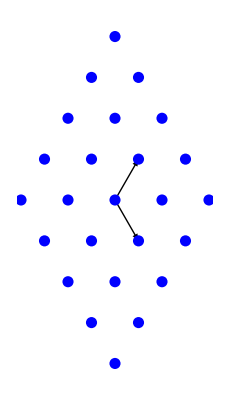

```mathematica
plotLattice[2,2,b1,b2,Blue]
```

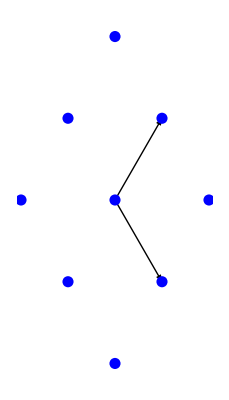

```mathematica
plotLattice[1,1,b1,b2,Blue]
```

```mathematica
find2DReciprocalLatticeBasisVector[a1_,a2_]:=Module[{},
d3a1=Flatten[{a1,0}];
d3a2=Flatten[{a2,0}];
d3a3={0,0,1};
d3b1=2π Cross[d3a2,d3a3]/(d3a1.Cross[d3a2,d3a3]);
d3b2=2π Cross[d3a3,d3a1]/(d3a2.Cross[d3a3,d3a1]);
b1=Drop[d3b1,-1];
b2=Drop[d3b2,-1];
{b1,b2}
]
plotBLVAndRLV2D[nn1_,nn2_,a1_,a2_]:=Module[{n1=nn1,n2=nn2},
{b1,b2}=find2DReciprocalLatticeBasisVector[a1,a2];
Print[b1/(2π)];
Print[b2/(2π)];
Print[√((b2/(2π)).(b2/(2π)))];
tableBLV=Flatten[Table[Table[m1 a1+m2 a2,{m1,-n1,n1}],{m2,-n2,n2}],1];
tableRLV=Flatten[Table[Table[m1 b1+m2 b2,{m1,-n1,n1}],{m2,-n2,n2}],1];
p0={0,0};
{{
Graphics[{
Arrow[{p0,a1}],
Arrow[{p0,a2}],
{Red,Point[tableBLV]}},PlotLabel->"Bravais lattice vectors"],
Graphics[{
Arrow[{p0,b1}],
Arrow[{p0,b2}],
{Blue,Point[tableRLV]}},PlotLabel->"Bravais lattice vectors"]
}}//TableForm
]
```

{1,-1/(√3)}

{0,2/(√3)}

2/(√3)

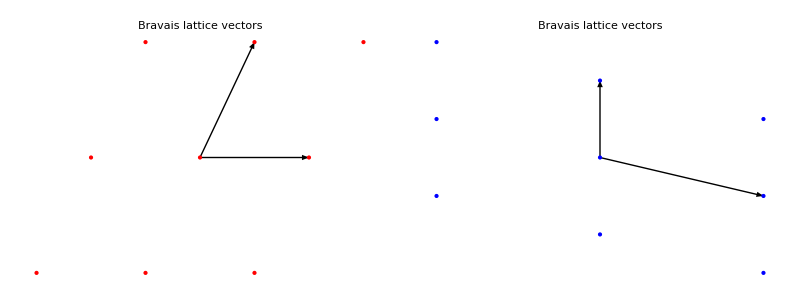

```mathematica
plotBLVAndRLV2D[1,1,{1,0},{1/2,(√3)/2}]
```

{1,1/(√3)}

{1,-1/(√3)}

2/(√3)

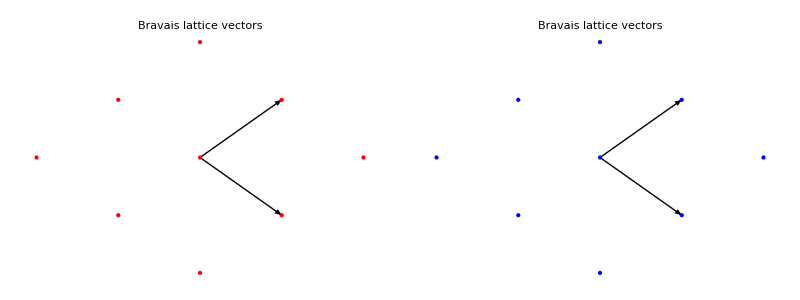

```mathematica
plotBLVAndRLV2D[1,1,{1/2,(√3)/2},{1/2,-(√3)/2}]
```

```mathematica
plotBLVAndRLV2D[1,1,{(√3)/2,1/2},{(√3)/2,-1/2}]
```

{1/(√3),1}

{1/(√3),-1}

2/(√3)

-Graphics-